```mathematica
β[ω_,δ_,t_,ϵ_,m_]:=ReplacePart[(ω+ⅈ*δ-ϵ)IdentityMatrix[m],Join[Table[{i,i-1},{i,Range[2,m,1]}],Table[{i,i+1},{i,Range[1,m,1]}]]->t]
```

```mathematica
T1[t_,m_]:= Module[{K=0*IdentityMatrix[m]},ReplacePart[K,Table[{x,x},{x,2,m,2}]->t]]
```

```mathematica
T2[t_,m_]:=t*IdentityMatrix[m]-T1[t,m]
```

```mathematica
Clear[LEFT]
```

```mathematica
leads =Table[ToExpression[Import["~/PhD_new/PhD/fwi/AGNR/sudo_q/leads0001/lead_"<>ToString[x]<>"_.dat"]],{x,Range[0,3,0.01]}]
```

{{{0.-0.000822461 ⅈ,0.582737+0. ⅈ,0.+0.000239724 ⅈ,-0.24829+0. ⅈ,0.+8.56628×10^-6 ⅈ,0.044418+0. ⅈ,0.-0.0000529843 ⅈ,0.0327459+0. ⅈ,0.+0.0000202384 ⅈ,-0.0288049+0. ⅈ,0.+8.56656×10^-6 ⅈ,0.00170892+0. ⅈ,0.-0.0000102755 ⅈ,0.00951467+0. ⅈ,0.+7.60799×10^-7 ⅈ},13,{0.+7.60799×10^-7 ⅈ,0.00951467+0. ⅈ,0.-0.0000102755 ⅈ,0.00170892+0. ⅈ,0.+8.56656×10^-6 ⅈ,-0.0288049+0. ⅈ,4,0.+8.56628×10^-6 ⅈ,-0.24829+0. ⅈ,0.+0.000239724 ⅈ,0.582737+0. ⅈ,0.-0.000822461 ⅈ}},299,{1}}
 |  |  |  |

```mathematica
LEFT[ω_,m_]:=LEFT[ω,m]=leads[[Round[ω*100+1]]](*Module[{J=Inverse[β[ω,0.001,1,0,m]],A:=Inverse[β[ω,0.001,1,0,m]],Ta:=T1[1,m],Tb= T2[1,m]},Do[J=Inverse[IdentityMatrix[m]-A.Tb.Inverse[IdentityMatrix[m]-A.Ta.J.Ta].A.Tb].A,5000];J=J]*)
```

```mathematica
f1[y_,start_,stop_]:= Table[{x,y},{x,start,stop}]
```

```mathematica
s[xstart_,xstop_,ystart_,ystop_]:=Module[{J=f1[ystart,xstart,xstop]},Do[J=Join[f1[y,xstart,xstop],J],{y,ystart+1,ystop}];J=J]
```

```mathematica
Clear[dist]
```

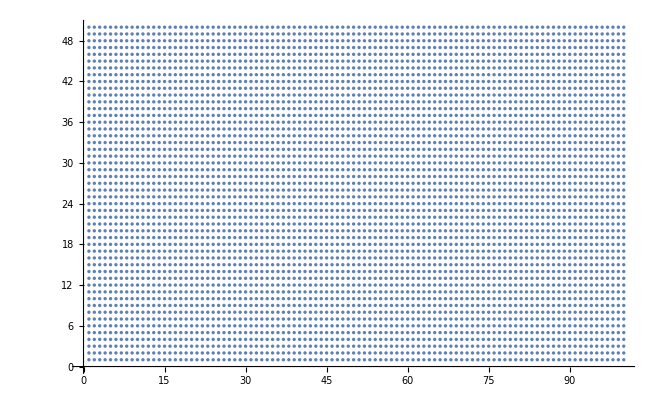

```mathematica
Join[s[1,50,1,Round[50/2]],s[51,100,50-Round[50/2]+1,50],Join[s[1,50,50-Round[50/2]+1,50],s[51,100,1,Round[50/2]]]]//ListPlot
```

```mathematica
dist[total_,concentration_,area_]:=dist[total,concentration,area]=Table[SortBy[Join[RandomSample[Join[s[1,50,1,Round[area/2]],s[51,100,area-Round[area/2]+1,area]],concentration],RandomSample[Join[s[1,50,area-Round[area/2]+1,area],s[51,100,1,Round[area/2]]],total-concentration]],First],10000]
```

```mathematica
f[ω_,δ_,t_,ϵ_,ϵ1_,area_,total_,concentration_,number_,unitcell_]:=Inverse[Module[{J=β[ω,δ,t,ϵ,area]},Do[J=Module[{m=unitcell},If[dist[total,concentration,area][[number]][[loc1,1]]==m,ReplacePart[J,{{dist[total,concentration,area][[number]][[loc1,2]],dist[total,concentration,area][[number]][[loc1,2]]}}->ω+ⅈ*δ-ϵ1],J]],{loc1,total}];J]]
```

```mathematica
f[0,0.001,1,0,0,51,100,50,1,2]
```

{{0.-38.4697 ⅈ,0.96153+0. ⅈ,0.+38.4687 ⅈ,-0.923062+0. ⅈ,0.-38.4678 ⅈ,0.884594+0. ⅈ,0.+38.4669 ⅈ,-0.846127+0. ⅈ,0.-38.4661 ⅈ,0.807661+0. ⅈ,0.+38.4653 ⅈ,-0.769195+0. ⅈ,0.-38.4645 ⅈ,0.730731+0. ⅈ,0.+38.4638 ⅈ,22,0.269203+0. ⅈ,0.+38.458 ⅈ,-0.230745+0. ⅈ,0.-38.4578 ⅈ,0.192287+0. ⅈ,0.+38.4576 ⅈ,-0.153829+0. ⅈ,0.-38.4574 ⅈ,0.115372+0. ⅈ,0.+38.4573 ⅈ,-0.0769145+0. ⅈ,0.-38.4573 ⅈ,0.0384572+0. ⅈ,0.+38.4572 ⅈ},49,{1}}
 |  |  |  |

```mathematica
TL[t_,m_,area_]:=Module[{MAT=0*IdentityMatrix[area]},MAT[[1;;m,1;;m]]=T1[t,m];MAT]
```

```mathematica
TR[t_,m_,area_]:=Module[{MAT=0*IdentityMatrix[area]},MAT[[area-m+1;;area,area-m+1;;area]]=T1[t,m];MAT]
```

```mathematica
SLLEAD[ω_,m_,area_]:=Module[{MAT=0*IdentityMatrix[area]},MAT[[1;;m,1;;m]]=LEFT[ω,m];MAT]
```

```mathematica
SRLEAD[ω_,m_,area_]:=Module[{MAT=0*IdentityMatrix[area]},MAT[[area-m+1;;area,area-m+1;;area]]=LEFT[ω,m];MAT]
```

```mathematica
CA[ω_,δ_,t_,ϵ_,ϵ1_,total_,concentration_,number_,m_,area_]:= Module[{},
recurs=Module[{J1=SLLEAD[ω,m,area]},
Do[
J1=Inverse[IdentityMatrix[area]-f[ω,δ,t,ϵ,ϵ1,area,total,concentration,number,unitcell+1].T2[t,area].Inverse[IdentityMatrix[area]-f[ω,δ,t,ϵ,ϵ1,area,total,concentration,number,unitcell].T1[t,area].J1.T1[t,area]].f[ω,δ,t,ϵ,ϵ1,area,total,concentration,number,unitcell].T2[t,area]].f[ω,δ,t,ϵ,ϵ1,area,total,concentration,number,unitcell+1],{unitcell,1,100,2}];J1=J1];ir=Inverse[IdentityMatrix[area]-SRLEAD[ω,m,area].TR[1,m,area].recurs.TR[1,m,area]].SRLEAD[ω,m,area];il=Inverse[IdentityMatrix[area]-recurs.TR[1,m,area].SRLEAD[ω,m,area].TR[1,m,area]].recurs;
gdd1= il-ConjugateTranspose[il];
grr1= ir-ConjugateTranspose[ir];
Gnonlocalrl=ir.TR[1,m,area].recurs;
GNON1= Gnonlocalrl-ConjugateTranspose[Gnonlocalrl];TRA=Abs[Tr[gdd1.TR[1,m,area].grr1.TR[1,m,area]-TR[1,m,area].GNON1.TR[1,m,area].GNON1]];If[TRA>10,10,TRA]]
```

```mathematica
Monitor[Table[Mean[ParallelTable[CA[0.85,0.001,1,0,1,70,x,number,15,51],{number,1000}]],{x,10,50,5}],x]
```

{2.51084,2.44816,2.30469,2.24537,2.2234,2.12601,2.07441,2.0619,1.94871}

```mathematica
Table[Mean[%22[[x]]],{x,9}]
```

{3.1911,3.09209,2.99236,2.90103,2.78709,2.65347,2.55854,2.46372,2.41621}

```mathematica
ListLinePlot[Table[ParallelTable[{ω,CA[ω,0.001,1,0,0,100,40,1,15,51]},{ω,Range[0,3,0.01]}],1]]
```

```mathematica
Monitor[Table[Export["~/PhD_new/PhD/fwi/AGNR/sudo_q/new_total_100_lead_15_diaglead_device_50_length_100_up_"<>ToString[conc]<>"_.dat",Monitor[Table[{ω,Mean[ParallelTable[CA[ω,0.001,1,0,1,100,conc,num,15,50],{num,1000}]]},{ω,Range[0,3,0.01]}],ω]],{conc,10,70,10}],conc]
```

$Aborted

```mathematica
transmission=Table[Import["~/PhD_new/PhD/fwi/AGNR/sudo_q/new_total_100_lead_15_diaglead_device_50_length_100_up_"<>ToString[x]<>"_.dat"],{x,10,60,10}]
```

```mathematica
input =Monitor[ParallelTable[Table[{ω, CA[ω,0.001,1,0,1,100,40,num,15,50]},{ω,Range[0,3,0.01]}],{num,10}],num]
```

{{{0.,1.96218},{0.01,0.011366},{0.02,0.0123806},{0.03,1.59497},{0.04,0.0433439},{0.05,0.0111406},{0.06,0.00447175},{0.07,0.00278735},{0.08,0.0018913},{0.09,0.00178469},{0.1,0.000564748},{0.11,0.00120701},{0.12,0.00444554},{0.13,0.0150721},274,{2.88,0.626965},{2.89,0.325072},{2.9,0.44611},{2.91,0.462026},{2.92,5.2006},{2.93,8.02955},{2.94,1.899},{2.95,0.950948},{2.96,0.875064},{2.97,1.62304},{2.98,1.08868},{2.99,1.42721},{3.,7.72223}},8,{1}}
 |  |  |  |

```mathematica
Table[Mean[ParallelTable[CA[2.29,0.001,1,0,1,100,conc,num,15,50],{num,1000}]],{conc,10,70,10}]
```

{1.54745,1.58961,1.62017,1.72296,1.79376,1.88421,1.98733}

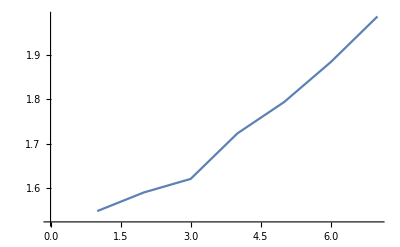

```mathematica
ListLinePlot[%40]
```

```mathematica
Clear[transmission]
```

```mathematica
transmission:=transmission=Monitor[Table[{x,Import["~/PhD_new/PhD/fwi/AGNR/sudo_q/new_total_100_lead_15_diaglead_device_50_length_100_up_"<>ToString[x]<>"_.dat"]},{x,Range[10,60,10]}],x]
```

```mathematica
input=Monitor[Table[Export["~/PhD_new/PhD/fwi/AGNR/sudo_q/example_30_"<>ToString[number]<>"_.dat",ParallelTable[{ω,CA[ω,0.001,1,0,1,100,30,number,15,50]},{ω,Range[0,2,0.01]}]],{number,100}],number]
```

```mathematica
input= Table[Import["~/PhD_new/PhD/fwi/AGNR/sudo_q/example_30_"<>ToString[x]<>"_.dat"],{x,100}]
```

{1}
 |  |  |  |

```mathematica
Table[{transmission[[x,1]],Module[{B1=Transpose[{input[[1]][[1;;301]][[;;,1]],(input[[1]][[1;;301,2]]-transmission[[x]][[2]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,2}]/((2-0)*100)]},{x,5}]
```

{{10,0.0121406},{20,0.0110311},{30,0.01015},{40,0.00924548},{50,0.00884452}}

```mathematica
misfit[x_,y_,n_]:=Module[{m5=input[[n]]},
ρ1:=Table[{transmission[[vvv,1]],Module[{B1=Transpose[{m5[[1;;301]][[;;,1]],(m5[[1;;301,2]]-transmission[[vvv]][[2]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)]},{vvv,5}];
list=ρ1;{list,list[[Position[list,Min[list]][[1,1]]]][[1]]}]
```

```mathematica
Table[misfit[1,0,n][[2]],{n,10}]
```

{40,20,10,50,10,10,50,20,50,50}

```mathematica
ListLinePlot[]
```

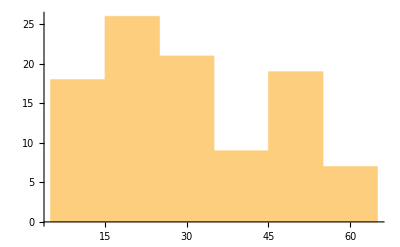

```mathematica
Histogram[%52]
```